```mathematica
Λ[t_,b_,d_]:=Max[{0,Min[{t-b,d-t}]}]
λ[t_,k_,bd_]:=Module[{l={},i=1},
For[i=1,i≤Length[bd],i++,AppendTo[l,Λ[t,bd[[i]][[1]],bd[[i]][[2]]]]];
Return[Sort[l,(#1>#2)&][[k]]]]
```

```mathematica
bd={{0.7596,1.5781},{0.0000,0.7571},{0.0000,0.6946},{0.0000,0.6360},{0.0000,0.6357},{0.0000,0.6119},{0.0000,0.5906},{0.0000,0.4604},{0.0000,0.3413},{0.0000,0.1942},{0.0000,0.1603},{0.0000,0.1360},{0.0000,0.1140},{0.0000,0.0500},{0.0000,0.0447},{0.0000,0.0361}}
```

{{0.7596,1.5781},{0.,0.7571},{0.,0.6946},{0.,0.636},{0.,0.6357},{0.,0.6119},{0.,0.5906},{0.,0.4604},{0.,0.3413},{0.,0.1942},{0.,0.1603},{0.,0.136},{0.,0.114},{0.,0.05},{0.,0.0447},{0.,0.0361}}

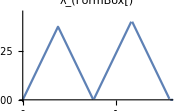
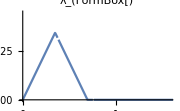
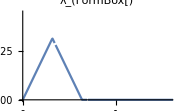
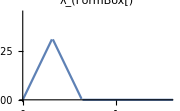
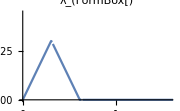
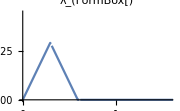
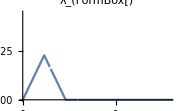
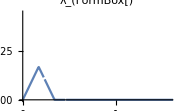

```mathematica
Table[Plot[λ[k,i,bd],{k,0,Length[bd]}, PlotRange->{{Min[bd],Max[bd]},{0,0.45}}, ImageSize-> Small, PlotLabel->Style[StringForm["λ_(``)", i], FontSize->14, FontWeight->Bold]],{i,1,Length[bd]}]
```

```mathematica
functions = Table[λ[k,i,bd], {i,1,Length[bd]}];
legends = Table[StringForm["λ_(``)", i],{i,1,Length[bd]}];
```

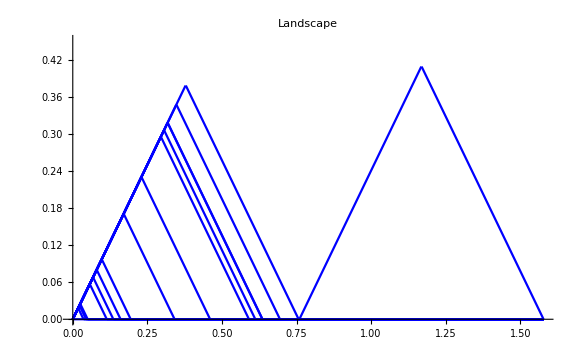

```mathematica
r = Plot[functions,{k,Min[bd],Max[bd]}, PlotRange->{{Min[bd],Max[bd]},{0,0.45}}, PlotStyle->Blue, ImageSize->Large, PlotLabel->"Landscape"]
```